```mathematica
psi[energy_?NumericQ]:={#[[1]],#[[1]][If[Length[#[[2]]]==0,100,#[[2,1,1]]]]}&@Reap[Block[{psi},NDSolveValue[{-1/2 psi''[x]+1/2 x^2*psi[x]==energy*psi[x],psi[0]==0,psi[1]==1,WhenEvent[Abs[psi[x]]>10,{Sow[x],"StopIntegration"}]},psi,{x,0,100}]]]
```

```mathematica
psi[0]
```

{InterpolatingFunction[…],10.}

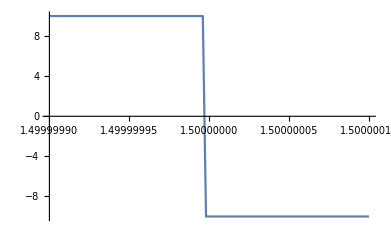

```mathematica
Plot[psi[e][[2]],{e,1.5-1*^-7,1.5+1*^-7}]
```

```mathematica
s=FindRoot[psi[e][[2]]==0,{e,3,4}][[1,2]]
```

Part::partw: psi[e] 的部分 2 不存在.

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

3.5

```mathematica
psi[s]
```

{InterpolatingFunction[…],10.}

```mathematica
s//InputForm
```

1.4999999965333044

```mathematica
fpsi=psi[s][[1]]
```

InterpolatingFunction[…]

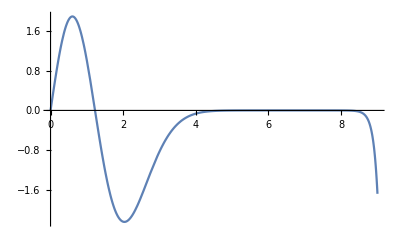

```mathematica
Plot[fpsi[x],{x,0,9}]
```